```mathematica
{$Version,Date[]}
```

{11.3.0 for Microsoft Windows (64-bit) (March 7, 2018),{2018,4,25,15,6,59.659011}}

RM: todo (?) :Lighting is different to 5.2 (completely different ...) .
     I added Glow as an option.

# The package Spinors.m

Bernd Thaller
Institute of Mathematics
University of Graz
Austria
2006-08-08

### Abstract

The package VQM`Spinors defines basic operations in the two-dimensional complex Hilbert space of a qubit. It defines the Pauli matrices and provides tools to visualize pure and mixed states of a qubit. This package is part of the VQM packages which can be obtained here:  http://www.uni-graz.at/imawww/vqm/software.html (free download). The VQM packages are part of the Visual Quantum Mechanics project, see http://www.uni-graz.at/imawww/vqm/. In particular, these packages are distributed with the book Advanced Visual Quantum Mechanics, Springer-Verlag New York, 2004.

## Load package

```mathematica
Needs["VQM`"];
```

This also loads the package "VQM`VisualizeVector".

## Bases

A spinor is a complex two-dimensional vector {c_1,c_2}, c_i ϵ ℂ, that is, an element of the linear space ℂ^2. The spinors are usually defined with respect to a reference basis in ℂ^2. The package defines the canonical standard basis

```mathematica
$QSpinBasis
```

{{1,0},{0,1}}

The basis spinors are interpreted as "spin-up" and "spin-down" with respect to the z-axis of a Cartesian basis in ℝ^3.

Other standard bases provided by the package are QxBasis, QyBasis, and QzBasis (QzBasis is equal to $QSpinBasis). For example, QxBasis consists of up and down spinors with respect to the x-axis:

```mathematica
QxBasis
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

Note that the symbols defined by the VQM packages all start with the letter Q in order to prevent conflicts with existing symbols defined in Mathematica or in other third-party packages.

The package also defines QSpinBasis as a default basis for some basis-dependent commands. It is initially equal to $QSpinBasis, but can be changed with the command QSetSpinBasis[{basespinor1,basespinor2}]. This influences how the components of spinors are calculated.

```mathematica
QSetSpinBasis[QxBasis];
QSpinBasis
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

An example of an operation that depends on the chosen basis is the calculation of the components of a spinor with respect to that basis. This is done with the command QSpinorToComponents. The spinor psi is given with respect to the reference basis $QSpinBasis. QSpinorToComponents[psi] calculates the components of psi with respect to the basis QSpinBasis. This gives the components of the spinor {1,0} with respect to the previously set QSpinBasis:

```mathematica
components = QSpinorToComponents[{1,0}]
```

{1/(√2),-1/(√2)}

components.QSpinBasis returns the original spinor. More generally, QComponentsToSpinor takes two complex coefficients and forms the corresponding linear combination of the basis vectors in QSpinBasis. The result is the spinor in the canonical standard basis.

```mathematica
QComponentsToSpinor[components]
```

{1,0}

QProjectUp[psi] projects a spinor psi into the direction of the first basis vector of QSpinBasis,

```mathematica
QProjectUp[{1,0}]
```

{1/2,1/2}

QProjectDown[psi] gives the part proportional to the second basis vector. The sum of the two projections is the identity, that is,

```mathematica
sp = {1,I};
QProjectUp[sp]+QProjectDown[sp] == sp
```

True

QProbabilityUp[psi] gives the probability that the spinor has spin-up with respect to the QSpinBasis, QProbabilityDown[psi] gives the probability for spin down.

A natural method for the visualization of a spinor is to represent its components with respect to a basis by a bar diagram. The height of the bars gives the absolute value, and the color gives the phase of the component.

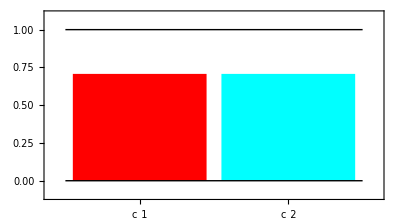

```mathematica
QSpinorBarDiagram[{1,0}]
```

Note that the image above shows the components {c_1,c_2} of the spinor with respect to the chosen QSpinBasis (= QxBasis). Let us restore the default setting. The following image then gives the components of the same spinor with respect to the canonical standard basis $QSpinBasis = QzBasis.

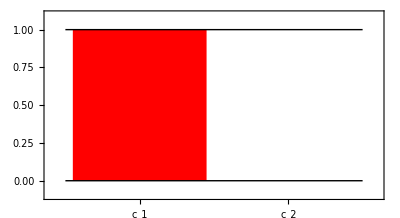

```mathematica
QSetSpinBasis[$QSpinBasis];
QSpinorBarDiagram[{1,0}]
```

All the commands above accept the option QUseBasis. You can use this option when you want use a particular basis just for one command. The following command gives the spin-up part with respect to the QyBasis of the spinor {1,-1}.

```mathematica
QProjectUp[{1,-1},QUseBasis->QyBasis]
```

{1/2+ⅈ/2,-1/2+ⅈ/2}

```mathematica
QSpinorToComponents[{1,-1}, QUseBasis->QxBasis]
```

{0,-√2}

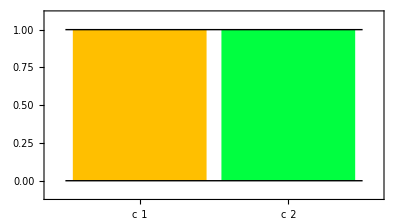

```mathematica
QSpinorBarDiagram[{1,-1}, QUseBasis->QyBasis]
```

You can compute the norm of a spinor with

```mathematica
Norm[{2,-I}]
```

√5

and QNormalize returns a spinor with norm 1

```mathematica
QNormalize[{2,-I}]
```

{2/(√5),-ⅈ/(√5)}

```mathematica
Norm[%]
```

1

The function QNormalize can also be used to normalize arbitrary vectors

```mathematica
QNormalize[{1,2,3}]
```

{1/(√14),√(2/7),3/(√14)}

## Some matrices

The package "VQM`Spinors" also defines the some important operators. First of all, we have the Pauli spin matrices QPauliSigma1, QPauliSigma2, and QPauliSigma3. Moreover, QPauliSigmaV is a vector with the three Pauli matrices as components

```mathematica
QPauliSigma2//MatrixForm
```

(0 | -ⅈ
ⅈ | 0)

```mathematica
QPauliSigmaV
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

The two-by-two identity matrix is QIdentity2. The Pauli sigma matrices are the quantum-mechanical observables for the spin measured with respect to the x-, y-, and z-axis of the reference coordinate system in ℝ^3. The spin-observable with respect to an arbitrary axis (represented by a vector kv) is QSpinHamiltonian[kv]. This matrix is obtained as
 QPauliSigma1.kv[[1]]+QPauliSigma2.kv[[2]]+QPauliSigma3.kv[[3]]

This is a three-dimensional vector with symbolic components

```mathematica
Clear[k0, k1, k2, k3, kv];
kv = {k1,k2,k3};
```

```mathematica
hs=QSpinHamiltonian[kv]
```

{{k3,k1-ⅈ k2},{k1+ⅈ k2,-k3}}

A density matrix is a hermitian matrix with trace 1. It is also determined by a vector in ℝ^3:

This is the density matrix describing spin in the direction of kv

```mathematica
ma = QVectorToDensityMatrix[kv]
```

{{(1+k3)/2,1/2 (k1-ⅈ k2)},{1/2 (k1+ⅈ k2),(1-k3)/2}}

```mathematica
ma//MatrixForm
```

((1+k3)/2 | 1/2 (k1-ⅈ k2)
1/2 (k1+ⅈ k2) | (1-k3)/2)

A four-vector {k0,k1,k2,k3} can be converted into a Hermitian matrix by:

```mathematica
QVectorToHermitianMatrix[{k0,k1,k2,k3}]
```

{{k0+k3,k1-ⅈ k2},{k1+ⅈ k2,k0-k3}}

and a three-vector {k1,k2,k3} by

```mathematica
QVectorToHermitianMatrix[{k1,k2,k3}]
```

{{k3,k1-ⅈ k2},{k1+ⅈ k2,-k3}}

which is the same as QSpinHamiltonian[{k1,k2,k3}]

There is also an inverse operation which determines the vector from a Hermitian matrix:

QHermitianMatrixToVector is inverse to QVectorToHermitianMatrix:

QDensityMatrixToVector is inverse to QVectorToDensityMatrix:

```mathematica
QHermitianMatrixToVector[QVectorToHermitianMatrix[{k0,k1,k2,k3}]] // Simplify
```

{k0,k1,k2,k3}

```mathematica
QDensityMatrixToVector[QVectorToDensityMatrix[{k1,k2,k3}]] // Simplify
```

{k1,k2,k3}

```mathematica
ma == QVectorToDensityMatrix[QDensityMatrixToVector[ma]] //Simplify
```

True

## The spinors QSpinorUp and QSpinorDown

The package defines two basis spinors for each direction in ℝ^3. These spinors are QSpinorUp[vector] and QSpinorDown[vector]. Here 'vector ' defines the direction. These spinors are eigenvectors of the matrix QVectorToMatrix[vector].

```mathematica
Clear[k1, k2, k3, kv]; kv = {k1,k2,k3};
```

```mathematica
QVectorToDensityMatrix[kv].QSpinorUp[kv] == Sqrt[kv.kv] QSpinorUp[kv]//Simplify
```

{-(k1^2+k2^2+(-1+k3) (k3+√(k1^2+k2^2+k3^2)))/(2 √2 √(k1^2+k2^2+k3 (k3+√(k1^2+k2^2+k3^2)))),-((k1+ⅈ k2) (-1+√(k1^2+k2^2+k3^2)))/(2 √2 √(k1^2+k2^2+k3 (k3+√(k1^2+k2^2+k3^2))))}=={0,0}

```mathematica
QVectorToHermitianMatrix[kv].QSpinorDown[kv] == -Sqrt[kv.kv] QSpinorDown[kv]//Simplify
```

True

Hence, for example, QSpinorUp[vector] is the state with spin-up in the direction of 'vector'. The two spinors form an orthonormal basis in ℂ^2. For example,

```mathematica
QConjSpinorUp[kv].QSpinorUp[kv]//Simplify
```

1

```mathematica
QConjSpinorDown[kv].QSpinorUp[kv]//Simplify
```

0

The conjugate comples spinors QConjSpinorUp[kv] and QConjSpinorDown[kv] have been defined for convenience.

We also note that QSpinorUp[kv] has a phase discontinuity on the negative z-axis, and QSpinorDown[kv] has a phase discontinuity on the positive z-axis.

```mathematica
QSpinorUp[{0,0,-1}]
```

{0,1}

```mathematica
Limit[QSpinorUp[{eps,0,-1}],eps->0]
```

{0,Indeterminate}

```mathematica
Limit[QSpinorUp[{-eps,0,-1}],eps->0]
```

{0,Indeterminate}

```mathematica
Limit[QSpinorUp[{0,eps,-1}],eps->0]
```

{0,Indeterminate}

## Spinors and Vectors

Consider the unit vector in three-dimensional space

```mathematica
vec = {-4/9,8/9,-1/9}
```

{-4/9,8/9,-1/9}

It defines a direction in space. The state which is "spin-up" with respect to this direction is

```mathematica
sp = QSpinorUp[vec]
```

{2/3,-1/3+(2 ⅈ)/3}

We can convert this spinor back to the vector

```mathematica
QSpinorToVector[sp]
```

{-4/9,8/9,-1/9}

The norm (length) of the three-dimensional real vector QSpinorToVector[spinor] is equal to  Norm[spinor]^2, that is

```mathematica
Norm[QSpinorToVector[{3,2}]] == Norm[{3,2}]^2
```

True

The command QSpinorToVector accepts the option QVectorLength

QSpinorToVector[psi, QVectorLength->n] with
n=1			generates a unit vector
n=2			generates a vector with norm Norm[psi]^2 (default)
n=3			generates a vector with norm Norm[psi]

There is also an inverse command QVectorToSpinor that accepts the same option.

QVectorToSpinor[vec, QVectorLength->n] with the option
n=1			generates a unit spinor
n=2			generates a vector with norm Norm[vec]^1/2 (default)
n=3			generates a vector with norm Norm[vec]

We have QVectorToSpinor[vec, QVectorLength->1] == QSpinorUp[vec].

## QExtractPhase

Note that the relation between spinors and vectors is not one-to-one. Here is another normalized spinor that gives the same vector than the spinor sp above:

```mathematica
sp2 =  {2/3,2 I/3-1/3}
```

{2/3,-1/3+(2 ⅈ)/3}

```mathematica
QSpinorToVector[sp2]
```

{-4/9,8/9,-1/9}

Generally, two spinors differing by a phase, sp1=Exp[I phi] sp2, lead to the same vector.

QExtractPhase[psi] returns a real number for any nonzero psi={z1,z2}. This number is a phase determined from comparison with QSpinorUp, where QSpinorUp is taken with respect to the spin-up direction defined by psi. Let us illustrate this with an example:

```mathematica
psi = QNormalize[{-2 I,1}]
```

{-(2 ⅈ)/(√5),1/(√5)}

This spinor has the spin-up direction (unit vector)

```mathematica
dir = QSpinorToVector[psi]
```

{0,4/5,3/5}

Note, however, that QSpinorUp[dir] is different from psi

```mathematica
QSpinorUp[dir]
```

{2/(√5),ⅈ/(√5)}

but the difference is only a phase factor. The phase can be obtained with QExtractPhase:

```mathematica
ph = QExtractPhase[psi]
```

-π/2

psi can now be recovered by multiplying QSpinorUp[dir] with the appropriate phase factor

```mathematica
Exp[I ph] QSpinorUp[dir]
```

{-(2 ⅈ)/(√5),1/(√5)}

Any spinor psi is thus uniquely determined by a three-dimensional vector together with phase factor.

## Rotations

QRotationSO3[vector] and QRotationSU2[vector] define rotations around the axis given by vector through an angle given by Norm[vector]. The matrix QRotationSO3[vector] is an orthogonal 3x3-matrix. QRotationSU2[vector] is a unitary 2x2 matrix realizing the 'spinor representation' of the rotation group.

For example,

```mathematica
QRotationSU2[{2 Pi,0,0}]//MatrixForm
```

(-1 | 0
0 | -1)

```mathematica
QRotationSU2[{1,1,1}]//MatrixForm
```

(Cos[(√3)/2]-(ⅈ Sin[(√3)/2])/(√3) | -((1+ⅈ) Sin[(√3)/2])/(√3)
((1-ⅈ) Sin[(√3)/2])/(√3) | Cos[(√3)/2]+(ⅈ Sin[(√3)/2])/(√3))

The textbook-form of the SU(2)-rotation matrix can be obtained as follows. Let us first define a unit vector with symbolic components.

```mathematica
Clear[nv,n1,n2,n3];
nv = {n1,n2,n3}; (* should be a unit vector *)
```

```mathematica
QRotationSU2[phi nv] // Simplify[#,{phi>0,nv.nv==1}]&
```

{{Cos[phi/2]-ⅈ n3 Sin[phi/2],-ⅈ (n1-ⅈ n2) Sin[phi/2]},{(-ⅈ n1+n2) Sin[phi/2],Cos[phi/2]+ⅈ n3 Sin[phi/2]}}

This matrix is the same as the following:

```mathematica
MatrixExp[-I phi/2 QVectorToHermitianMatrix[nv]] // ExpToTrig // Simplify[#,{phi>0,nv.nv==1}]&
```

{{Cos[phi/2]-ⅈ n3 Sin[phi/2],(-ⅈ n1-n2) Sin[phi/2]},{(-ⅈ n1+n2) Sin[phi/2],Cos[phi/2]+ⅈ n3 Sin[phi/2]}}

Any unitary 2x2-matrix may be considered a SU(2) rotation. The following example shows the connection with a basis transformation

```mathematica
Clear[a,b];
T=QRotationSU2[{1,1,1}];
newBasis={T.QzBasis[[1]], T.QzBasis[[2]]};
QSpinorToComponents[{a,b},QUseBasis->newBasis] == Inverse[T].{a,b} // Simplify
```

True

The connection between rotations in SO(3) and rotations in SU(2) is the following:

```mathematica
rotV = {1, 0.5, -1};
R = QRotationSO3[rotV];
T = QRotationSU2[rotV];
```

```mathematica
QVectorToSpinor[ R . {1,0,0} ] == T . QVectorToSpinor[{1,0,0}]
```

True

```mathematica
QVectorToHermitianMatrix[ R . {1,0,0} ] == Chop[T . QVectorToHermitianMatrix[{1,0,0}] . Inverse[T]]
```

True

```mathematica
QVectorToArrow
```

QVectorToArrow

```mathematica
QVectorToArrow//Options
```

{QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0],QNeedleStyle→False}

## Visualization

```mathematica
coloroptt
```

coloroptt

Since spinors and Hermitian matrices can be converted into vectors, we can visualize them

```mathematica
??Glow
```

Glow[col] is a graphics directive which specifies that surfaces of 3D graphics objects that follow are to be taken to glow with color col. 
Glow[] specifies that there is no glow.

Attributes[Glow]={Protected,ReadProtected}

```mathematica
Graphics3D[QSpinorToArrow[{-I,1+I}]]
```

-Graphics3D-

```mathematica
Graphics3D[QSpinorToArrow[{ⅈ,1}]/.Hue[a__]:>Glow[Hue[a]],Lighting->Automatic]
```

-Graphics3D-

```mathematica
Options [Graphics3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→Automatic,BoxStyle→{},ClipPlanes→None,ClipPlanesStyle→Automatic,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,PlotLabel→None,PlotRange→All,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→False,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1}}

```mathematica
QSpinorToArrow[{1,1}]//Graphics3D
```

-Graphics3D-

The package VQM`VisualizeVector (which is loaded automatically by VQM`Spinors) provides all necessary commands for visualizing vectors. These commands are also used by VQM`Spinors for the visualization of spinors and Hermitian matrices..

The  commands QVectorToArrow and QSpinorToArrow return a 3D-graphics primitive describing an arrow whose properties are determined by the following options

```mathematica
Options[QVectorToArrow]
```

{QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0],QNeedleStyle→False}

QArrowHead->True (default) causes the vector to be drawn with an arrow head. QArrowHead->Automatic draws the vector with a point of size 2*QLinePointSize instead of the QArrowHead. Otherwise the vector is just represented by a line segment.

QMinLength->0.1 (default) specifies that vectors of length less than 0.1 are to be drawn as points of size QLinePointSize.

QArrowShape->{n,k}: The head of the arrow is a cone with half height h = k * Norm[vector] and radius r = h/(2 GoldenRatio) drawn using n polygons. If k is negative, then h = -k. Default is (1,1/6)

QArrowScale-> k scales the length of the arrow by the factor k.

QHeadColor->colordirective: The arrow appears in the color specified by colordirective. Turn Lighting off to see the effect.

QLinePointSize->pt  causes the shaft of the arrow to be drawn with relative pointsize pt. Default is  pt = 0.001.

QSpinorToArrow draws the arrow head by default in a color determined by the complex phase of the spinor. The options QHeadColor->QExtractPhase is also accepted. The complex phase factor Exp[I phase] is mapped to colors according to Hue[phase/(2 Pi)] (this is the standard color map of complex numbers).

Here are some examples:

```mathematica
Graphics3D[
	QVectorToArrow[{1,1,-1},
		QArrowShape->{12,1/3}, QLinePointSize->0.007]
]
```

-Graphics3D-

```mathematica
%//InputForm
```

Graphics3D[{{Thickness[0.007], Line[{{0, 0, 0}, {1, 1, -1}}]}, 
  {GrayLevel[1], {Polygon[{{1, 1, -1}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3 - 1/(2*Sqrt[6]*GoldenRatio), -2/3}, 
      {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(3*Sqrt[2]*GoldenRatio), -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(3*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}, {2/3, 2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3, 2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(3*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 
       2/3 - 1/(6*Sqrt[2]*GoldenRatio), -2/3 - 1/(3*Sqrt[2]*GoldenRatio)}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 - 1/(3*Sqrt[2]*GoldenRatio), 2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 - 1/(3*Sqrt[2]*GoldenRatio), 
       2/3 + 1/(6*Sqrt[2]*GoldenRatio), -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       2/3 + 1/(2*Sqrt[6]*GoldenRatio), -2/3}}], 
    Polygon[{{1, 1, -1}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3 + 1/(2*Sqrt[6]*GoldenRatio), -2/3}, 
      {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(3*Sqrt[2]*GoldenRatio), -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(3*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}, {2/3, 2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3, 2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(3*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       2/3 + 1/(6*Sqrt[2]*GoldenRatio), -2/3 + 1/(3*Sqrt[2]*GoldenRatio)}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 + 1/(3*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 + 1/(3*Sqrt[2]*GoldenRatio), 
       2/3 - 1/(6*Sqrt[2]*GoldenRatio), -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       2/3 - 1/(2*Sqrt[6]*GoldenRatio), -2/3}}]}}}]

```mathematica
Graphics3D[{{Thickness[0.007], Line[{{0, 0, 0}, {1, 1, -1}}]}, 
  {White, {Polygon[{{1, 1, -1}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(3*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       2/3 - 1/(3*Sqrt[2]*GoldenRatio), -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}, 
      {2/3, 2/3 - 1/(2*Sqrt[6]*GoldenRatio), -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3, 2/3 - 1/(2*Sqrt[6]*GoldenRatio), -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}, 
      {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), -2/3 - 1/(3*Sqrt[2]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(3*Sqrt[2]*GoldenRatio)}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3, 
       -2/3 - 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 - 1/(3*Sqrt[2]*GoldenRatio), 2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 - 1/(3*Sqrt[2]*GoldenRatio), 
       2/3 + 1/(6*Sqrt[2]*GoldenRatio), -2/3 - 1/(6*Sqrt[2]*GoldenRatio)}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       2/3 + 1/(2*Sqrt[6]*GoldenRatio), -2/3}}], 
    Polygon[{{1, 1, -1}, {2/3 - 1/(2*Sqrt[6]*GoldenRatio), 2/3 + 1/(2*Sqrt[6]*GoldenRatio), -2/3}, 
      {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(3*Sqrt[2]*GoldenRatio), -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 - 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(3*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}, {2/3, 2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3, 2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(3*Sqrt[2]*GoldenRatio)}}], Polygon[{{1, 1, -1}, {2/3 + 1/(6*Sqrt[2]*GoldenRatio), 
       2/3 + 1/(6*Sqrt[2]*GoldenRatio), -2/3 + 1/(3*Sqrt[2]*GoldenRatio)}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 
       2/3, -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3, -2/3 + 1/(2*Sqrt[6]*GoldenRatio)}, 
      {2/3 + 1/(3*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}}], 
    Polygon[{{1, 1, -1}, {2/3 + 1/(3*Sqrt[2]*GoldenRatio), 2/3 - 1/(6*Sqrt[2]*GoldenRatio), 
       -2/3 + 1/(6*Sqrt[2]*GoldenRatio)}, {2/3 + 1/(2*Sqrt[6]*GoldenRatio), 2/3 - 1/(2*Sqrt[6]*GoldenRatio), 
       -2/3}}]}}},Lighting->Automatic]
```

-Graphics3D-

```mathematica
QVectorToArrow//Options
```

{QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0],QNeedleStyle→False}

```mathematica
Graphics3D[QVectorToArrow[{1,1,-1},QArrowShape->{12,1/3},QLinePointSize->0.02,Lighting->Automatic]]
```

-Graphics3D-

```mathematica
Options[QVectorToArrow]
```

{QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0],QNeedleStyle→False}

```mathematica
Graphics3D[QVectorToArrow[{1,1,-1},QArrowShape->{12,1/3},QLinePointSize->0.02,QHeadColor->Blue]]
```

-Graphics3D-

```mathematica
Graphics3D[QSpinorToArrow[ⅇ^((ⅈ π)/4) {1,1},Lighting->None],PlotRange->All]
```

-Graphics3D-

Finally, there are the commands QVisualizeVector, QVisualizeSpinor, and QVisualizeOperator. They convert their argument into an arrow which is then shown together with auxiliary graphics elements. The appearance of those auxiliary graphics elements is controlled by the following options

```mathematica
Options[QVisualizeVector]
```

{QDrawUnitSphere→18,QDrawAxes→True,QCoordinateCube→False,QCoordinateCircles→True,QCoordinateCirclesColor→RGBColor[0, 0, 1],QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0],QNeedleStyle→False}

```mathematica
Options[QVisualizeSpinor]
```

{QNeedleStyle→True,QDrawUnitSphere→18,QDrawAxes→True,QCoordinateCube→False,QCoordinateCircles→True,QCoordinateCirclesColor→RGBColor[0, 0, 1],QArrowHead→True,QArrowShaft→False,QLinePointSize→0.001,QMinLength→0.1,QArrowShape→Automatic,QHeadColor→GrayLevel[1],QArrowScale→1,QShaftColor→GrayLevel[0]}

This shows a spinor as a vector on the surface of the Bloch-sphere. The size and shape of the arrow is controlled by Options[QArrowToVector] as described above.

```mathematica
QVisualizeSpinor[QNormalize[(-1+I) {1 , 1+I}]]
```

-Graphics3D-

```mathematica
QVisualizeSpinor[QNormalize[(-1+I) {1 , 1+I}], QNeedleStyle->False]
```

-Graphics3D-

Additional graphics elements may sometimes be helpful

```mathematica
QVisualizeVector[{1,1,1}/Sqrt[3],QCoordinateCube->True, QCoordinateCircles->False, QDrawUnitSphere->10, QDrawAxes->{True,False,True}]
```

-Graphics3D-

A Density matrix can also be visualized as a vector.

```mathematica
dm = QVectorToDensityMatrix[{1.,-.5,2}//QNormalize]
```

{{0.936436,0.218218+0.109109 ⅈ},{0.218218-0.109109 ⅈ,0.0635642}}

```mathematica
QVisualizeDensityMatrix[dm, QArrowShape->{6,1/3}, QLinePointSize->.01]
```

-Graphics3D-

Options for QVisualizeVector, etc.

QDrawUnitSphere->n 		draws the outline of the unit sphere by plotting n (default: 20) circles.
QDrawAxes->True 			or, for example, QDrawAxes->{True, False, True} adds gray coordinate axes.
QCoordinateCube->->True 		adds a green cube indicating the components of the vector (default: False).
QCoordinateCircles->True 		adds blue coordinate lines indicating the polar coordinates of the vector.
QHeadColor->QExtractPhase	works only with QVisualizeSpinor, see QSpinorToArrow
QHeadColor->color			draws the vector with the given color